```mathematica
qLearnFile = FileNameJoin[{NotebookDirectory[],"qlearn.dat"}];
```

```mathematica
qLearnData=ReadList[qLearnFile, Number];
```

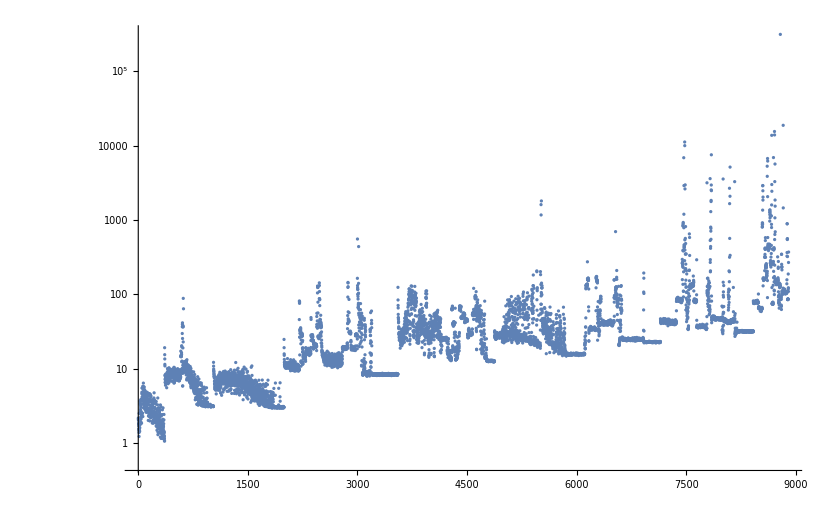

```mathematica
qLearnPlot=ListLogPlot[qLearnData, PlotRange->All]
```

```mathematica
Dynamic[ListLogPlot[ReadList["/home/byrdie/School/Classes/CSCI446_Artificial_Intelligence/CSCI446_Artificial_Intelligence_Project4_ReinforcementLearning/src/CSCI446_Project4_ReinforcementLearning/qlearn.dat", Number], PlotRange->All],UpdateInterval->1]
```